```mathematica
ϵ=10^-30
```

1/1000000000000000000000000000000

```mathematica
g[x_] = x*Sin[x^2]
```

x Sin[x^2]

```mathematica
g[x_] =Sin[x]
```

Sin[x]

```mathematica
D[g[x], x]
```

2 x^2 Cos[x^2]+Sin[x^2]

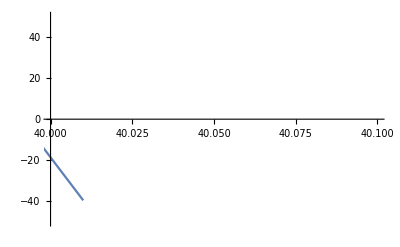

```mathematica
Plot[g[x],{x, -40, 40.01},PlotRange->{{40,40.1},{-50,50}}]
```

```mathematica
LinguisticAssistant
```

```mathematica
Subscript[x, 0]=40;Δx=1*10^-19;
```

```mathematica
N[g[Subscript[x, 0] + Δx] - g[Subscript[x, 0]],4]
```

-1.916×10^-16

```mathematica
N[g[Subscript[x, 0] + Δx] - g[Subscript[x, 0]] - Δx*D[g[x],x]/.x-> Subscript[x, 0],25]
```

1.024849695909872051876547×10^-33

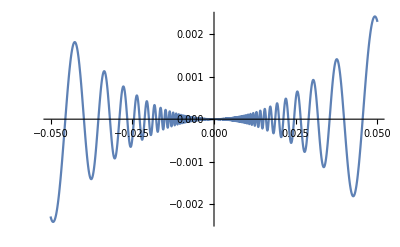

```mathematica
Plot[x^2*Sin[1/x],{x,-0.05,0.05}]
```

```mathematica
D[x^2*Sin[1/x], x]
```

-Cos[1/x]+2 x Sin[1/x]

```mathematica
f[x_] = x^2*Sin[1/x]
```

x^2 Sin[1/x]

```mathematica
x^2 Sin[1/x]
```

```mathematica
Subscript[x, 0]=0.0001; Δx=1*10^-8;
```

```mathematica
N[f[Subscript[x, 0]+Δx]-f[Subscript[x, 0]] - Δx*D[f[x],x]/.x-> Subscript[x, 0]]
```

-1.03428×10^-10

```mathematica
N[f[Subscript[x, 0]+Δx]-f[Subscript[x, 0]]]
```

9.41751×10^-9